# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.910113102752929×10^9

#### 変数

```mathematica
date="20231010"
```

20231010

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231010.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231010.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

21124901 293477497 9943356563 log-20231010.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{184333}

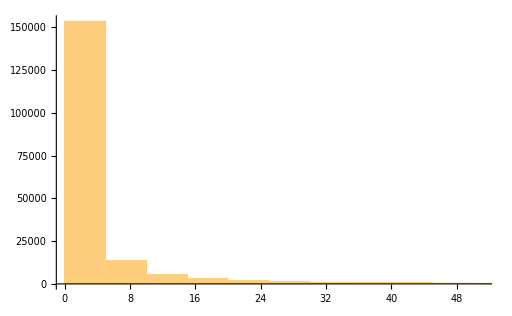

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{184333}

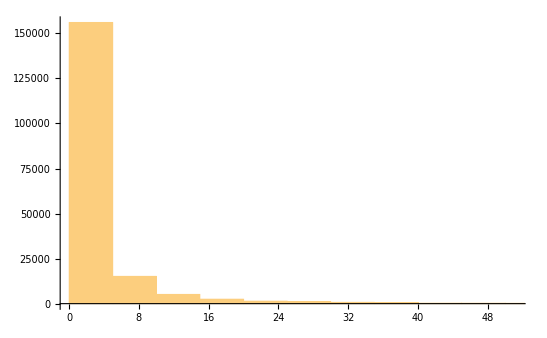

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{184333}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{184333}

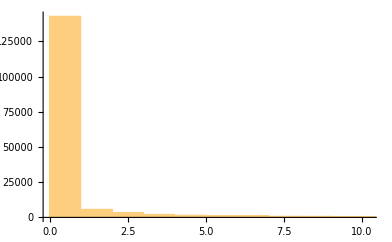

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{184333}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{184333}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{184333}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{184333}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{about:blank}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{41,55,56,71,74,90,95,97,124,157,195,207,225,251,252,253,254,256,257,258,259,260,270,319,328,343,408,409,443,463,467,508,660,699,760,762,766,870,872,877,911,913,914,1155,1163,1164,1196,1539,1639}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:kaken.nii.ac.jp,http:lms.nii.ac.jp,http:preview-jupyter.cs.rcos.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:ci-nii-ac-jp.libproxy.ouj.ac.jp,https:cir.nii.ac.jp,https:cir-nii-ac-jp.lib-kansai-u.idm.oclc.org,https:cir-nii-ac-jp.musashino-u.remotexs.co,https:cir-nii-ac-jp.swu.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:contents.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:kurume.repo.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:njc.repo.nii.ac.jp,https:nrid.nii.ac.jp,https:openidp.nii.ac.jp,https:operationhub.cs.rcos.nii.ac.jp,https:otsuma.repo.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp,https:stars.repo.nii.ac.jp,https:support-nii.ac.jp,https:support.nii.ac.jp,https:toyo-bunko.repo.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
niigrp=".*\\.nii\\.ac\\.jp.*"
```

.*\.nii\.ac\.jp.*

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[niigrp]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{184333}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,163030},{1,21297},{3,6}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,137073},{2,47258},{3,2}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1806,2}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{51,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 136766
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20888
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 25280
https:cir.nii.ac.jp
https:support.nii.ac.jp | 107
https:cir.nii.ac.jp
https:www.nii.ac.jp | 10
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 104
https:jdcat.jsps.go.jp | 68
https:lms.nii.ac.jp | 143
https:jupyter.cs.rcos.nii.ac.jp
https:meatwiki.nii.ac.jp | 3
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 483
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 239
http:kaken.nii.ac.jp
https:cir.nii.ac.jp | 2
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 15
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 6
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 31
https:jupyter.cs.rcos.nii.ac.jp | 96
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 13
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 8
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:toyo-bunko.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kurume.repo.nii.ac.jp | 2
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 6
https:cir.nii.ac.jp
https:otsuma.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 4
https:jdcat.jsps.go.jp
https:redmine.devops.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:cir.nii.ac.jp
https:idp.nii.ac.jp | 1
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 13
https:jupyter.cs.rcos.nii.ac.jp
https:operationhub.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:contents.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:contents.nii.ac.jp
https:lms.nii.ac.jp | 2
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 2
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 8
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 2
https:cir.nii.ac.jp
https:stars.repo.nii.ac.jp | 1
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
https:cir.nii.ac.jp
https:njc.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:openidp.nii.ac.jp | 1
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 3
https:cir.nii.ac.jp
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
http:preview-jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

4

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

4

```mathematica
Sort[accessTime["ci"]]//Length
```

1

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BinCounts[accessTime[ci],{4,4,600}]

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BinCounts[accessTime[cs],{4,4,600}]

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BinCounts[accessTime[la],{4,4,600}]

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

BinCounts[accessTime[wk],{4,4,600}]

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of BinCounts::vectmat will be suppressed during this calculation.

ListPlot::lpn: BinCounts[accessTime[ci],{4.,4.,600.}] is not a list of numbers or pairs of numbers.

ListPlot[BinCounts[accessTime[ci],{4,4,600}],PlotRange→Full,Joined→True]

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of BinCounts::vectmat will be suppressed during this calculation.

ListPlot::lpn: BinCounts[accessTime[cs],{4.,4.,600.}] is not a list of numbers or pairs of numbers.

ListPlot[BinCounts[accessTime[cs],{4,4,600}],PlotRange→Full,Joined→True]

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of BinCounts::vectmat will be suppressed during this calculation.

ListPlot::lpn: BinCounts[accessTime[la],{4.,4.,600.}] is not a list of numbers or pairs of numbers.

ListPlot[BinCounts[accessTime[la],{4,4,600}],PlotRange→Full,Joined→True]

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

General::stop: Further output of BinCounts::vectmat will be suppressed during this calculation.

ListPlot::lpn: BinCounts[accessTime[wk],{4.,4.,600.}] is not a list of numbers or pairs of numbers.

ListPlot[BinCounts[accessTime[wk],{4,4,600}],PlotRange→Full,Joined→True]

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{184333}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{121,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{16,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{121,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{121,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{5,32,7,42,19,104,5,33,2,4,9,6,13,2,6,17,2,6,11,51,2,25,24,99,88,85,19,9,2,39,37,7,13,57,23,9,49,17,38,215,198,10,24,23,26,71,19,22,22,21,7,9,20,25,67,6,17,13,12,11,15,21,11,276,280,272,26,32,8,6,31,189,185,192,3,11,11,44,45,46,14,31,24,24,23,37,106,105,111,106,40,41,45,6,89,14,16,13,5,312,312,318,11,15,2,6,46,45,2,12,22,8,5,2,20,19,295,325,296,296,15}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{33.,2865.,77.,1336.,355.,30117.,802.,8363.,0.,63.,2375.,87.,129.,0.,398.,424.,0.,845.,132.,939.,0.,2197.,2186.,28325.,28325.,28325.,809.,65.,0.,35263.,35243.,191.,1224.,2968.,1083.,135.,5853.,3134.,6724.,4130.,4020.,2001.,1352.,1337.,5001.,23452.,2040.,1440.,1428.,1428.,849.,174.,1783.,516.,15556.,359.,410.,1224.,11101.,11016.,341.,330.,34812.,24038.,28523.,23983.,19502.,3318.,30525.,1387.,1322.,23346.,15718.,15718.,15755.,437.,398.,14707.,14707.,16886.,531.,32477.,24369.,11254.,11254.,27442.,27437.,27293.,27446.,27293.,20280.,20342.,20280.,104.,24932.,2024.,2007.,1980.,78.,17635.,17635.,26961.,2223.,2059.,0.,17077.,35296.,35266.,0.,1288.,2939.,123.,114.,0.,645.,627.,8848.,8848.,8848.,8848.,331.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{121,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{888,1},{5043,1},{6086,1},{8845,1},{8949,1},{9492,1},{12443,1},{12903,1},{16925,1},{23064,1},{23722,1},{23826,1},{25863,1},{26350,1},{27216,1},{29045,1},{30166,1},{32289,1},{32493,1},{41688,1},{42374,1},{42580,1},{42580,1},{44627,1},{44627,1},{44627,1},{45238,1},{46599,1},{50267,1},{51540,1},{51540,1},{54147,1},{55078,1},{55874,1},{55947,1},{58827,1},{58830,1},{58858,1},{58876,1},{60551,1},{60551,1},{60551,1},{61029,1},{61029,1},{61055,1},{61599,1},{61608,1},{62578,1},{62578,1},{62578,1},{62799,1},{62945,1},{63338,1},{65312,1},{66102,1},{69213,1},{70632,1},{71995,1},{71999,1},{71999,1},{78100,1},{78100,1},{78110,1},{79940,1},{79940,1},{79940,1},{80300,1},{81313,1},{83213,1},{86213,1},{89927,1},{91299,1},{91299,1},{91299,1},{94703,1},{98403,1},{98403,1},{99551,1},{99551,1},{99551,1},{100421,1},{101044,1},{101044,1},{101044,1},{101044,1},{101343,1},{101693,1},{101693,1},{101693,1},{101693,1},{102713,1},{102713,1},{102713,1},{103863,1},{104318,1},{104422,1},{104422,1},{104422,1},{104778,1},{105480,1},{105480,1},{105480,1},{107743,1},{107743,1},{108958,1},{114524,1},{116845,1},{116845,1},{137416,1},{137477,1},{144638,1},{144806,1},{147618,1},{148333,1},{150444,1},{150444,1},{151376,1},{151376,1},{151376,1},{151376,1},{151962,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{5,32,7,42,19,104,5,33,2,4,9,6,13,2,6,17,2,6,11,51,2,25,24,99,88,85,19,9,2,39,37,7,13,57,23,9,49,17,38,215,198,10,24,23,26,71,19,22,22,21,7,9,20,25,67,6,17,13,12,11,15,21,11,276,280,272,26,32,8,6,31,189,185,192,3,11,11,44,45,46,14,31,24,24,23,37,106,105,111,106,40,41,45,6,89,14,16,13,5,312,312,318,11,15,2,6,46,45,2,12,22,8,5,2,20,19,295,325,296,296,15}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{8,53,7,96,44,163,7,41,1,3,12,9,16,1,12,42,1,8,15,87,1,62,50,178,129,142,35,12,1,66,51,8,22,75,38,10,83,21,63,323,302,16,52,47,46,128,38,54,45,44,12,10,30,35,99,7,18,20,17,16,17,23,14,396,412,404,49,40,10,5,46,325,311,311,2,15,13,67,68,74,20,45,41,40,35,66,308,284,297,286,51,52,58,6,133,28,29,25,4,501,503,547,20,16,1,10,75,67,1,22,30,11,7,1,34,29,984,1113,986,989,29}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{121}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0.25,24.5333,0.333333,2.48333,0.9,263.133,11.95,114.967,0,0.85,37.8167,0.483333,0.35,0,5.83333,1.,0,10.95,0.733333,1.81667,0,11.3167,11.3167,264.483,421.583,421.583,3.01667,0.25,0,339.933,340.083,1.83333,5.7,13.3167,12.0833,0.75,18.6667,23.2,32.7333,17.3833,17.3833,26.9833,15.15,15.15,36.5833,328.417,17.9,5.23333,5.05,5.23333,7.73333,1.13333,16.05,1.06667,70.8167,4.35,2.63333,15.,167.317,167.317,1.48333,0.916667,341.633,188.233,187.583,188.267,209.1,11.85,505.65,21.7,3.31667,176.35,202.117,202.117,262.583,4.58333,4.58333,121.767,121.767,119.033,4.18333,352.983,218.4,81.2667,81.2667,313.05,59.95,59.95,38.4,59.95,99.0333,99.0333,92.5167,0.816667,369.283,19.55,19.55,19.55,0.9,77.1667,77.1667,92.6333,31.8333,26.9167,0,260.967,294.817,294.817,0,9.53333,10.4167,0.666667,0.716667,0,2.13333,2.61667,39.9167,39.9167,39.9167,39.9167,1.8}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{33.,2865.,77.,1336.,355.,30117.,802.,8363.,0.,63.,2375.,87.,129.,0.,398.,424.,0.,845.,132.,939.,0.,2197.,2186.,28325.,28325.,28325.,809.,65.,0.,35263.,35243.,191.,1224.,2968.,1083.,135.,5853.,3134.,6724.,4130.,4020.,2001.,1352.,1337.,5001.,23452.,2040.,1440.,1428.,1428.,849.,174.,1783.,516.,15556.,359.,410.,1224.,11101.,11016.,341.,330.,34812.,24038.,28523.,23983.,19502.,3318.,30525.,1387.,1322.,23346.,15718.,15718.,15755.,437.,398.,14707.,14707.,16886.,531.,32477.,24369.,11254.,11254.,27442.,27437.,27293.,27446.,27293.,20280.,20342.,20280.,104.,24932.,2024.,2007.,1980.,78.,17635.,17635.,26961.,2223.,2059.,0.,17077.,35296.,35266.,0.,1288.,2939.,123.,114.,0.,645.,627.,8848.,8848.,8848.,8848.,331.}

```mathematica
staytimeCKAN/60
```

{0.55,47.75,1.28333,22.2667,5.91667,501.95,13.3667,139.383,0.,1.05,39.5833,1.45,2.15,0.,6.63333,7.06667,0.,14.0833,2.2,15.65,0.,36.6167,36.4333,472.083,472.083,472.083,13.4833,1.08333,0.,587.717,587.383,3.18333,20.4,49.4667,18.05,2.25,97.55,52.2333,112.067,68.8333,67.,33.35,22.5333,22.2833,83.35,390.867,34.,24.,23.8,23.8,14.15,2.9,29.7167,8.6,259.267,5.98333,6.83333,20.4,185.017,183.6,5.68333,5.5,580.2,400.633,475.383,399.717,325.033,55.3,508.75,23.1167,22.0333,389.1,261.967,261.967,262.583,7.28333,6.63333,245.117,245.117,281.433,8.85,541.283,406.15,187.567,187.567,457.367,457.283,454.883,457.433,454.883,338.,339.033,338.,1.73333,415.533,33.7333,33.45,33.,1.3,293.917,293.917,449.35,37.05,34.3167,0.,284.617,588.267,587.767,0.,21.4667,48.9833,2.05,1.9,0.,10.75,10.45,147.467,147.467,147.467,147.467,5.51667}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.keiho-u.ac.jp/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{121}

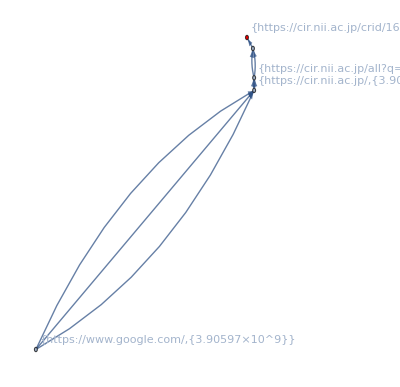

```mathematica
ckanGrPRselHLTL[4][[1]]
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

```mathematica
gr=ckanGrPRselHLTL[4][[1]]
```

-Graphics-

```mathematica
rl=vocRl["all:path"];
```

====== 引数/ ======

====== /内部変数 ======

```mathematica
vl=VertexList[gr]
```

{{https://www.google.com/,{3.90597×10^9}},{https://cir.nii.ac.jp/,{3.90597×10^9,3.90597×10^9,3.90597×10^9}},{https://cir.nii.ac.jp/all?q=Connected+Industries,{3.90597×10^9,3.90597×10^9}},{https://cir.nii.ac.jp/all?q=%E3%82%B3%E3%83%8D%E3%82%AF%E3%83%86%E3%83%83%E3%83%89%E3%82%A4%E3%83%B3%E3%83%80%E3%82%B9%E3%83%88%E3%83%AA%E3%83%BC%E3%82%BA&count=20&sortorder=0,{3.90597×10^9,3.90597×10^9}},{https://cir.nii.ac.jp/crid/1690857923906760064,{3.90597×10^9}}}

```mathematica
vname=Map[#[[1]]&,vl]
```

{https://www.google.com/,https://cir.nii.ac.jp/,https://cir.nii.ac.jp/all?q=Connected+Industries,https://cir.nii.ac.jp/all?q=%E3%82%B3%E3%83%8D%E3%82%AF%E3%83%86%E3%83%83%E3%83%89%E3%82%A4%E3%83%B3%E3%83%80%E3%82%B9%E3%83%88%E3%83%AA%E3%83%BC%E3%82%BA&count=20&sortorder=0,https://cir.nii.ac.jp/crid/1690857923906760064}

```mathematica
vrename=(vname/.rl)
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{https://www.google.com/,voc[ci:top],voc[ci:search/all],voc[ci:search/all],voc[ci:detail]}

```mathematica
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]]
```

{{https://www.google.com/,{3.90597×10^9}}→https://www.google.com/,{https://cir.nii.ac.jp/,{3.90597×10^9,3.90597×10^9,3.90597×10^9}}→voc[ci:top],{https://cir.nii.ac.jp/all?q=Connected+Industries,{3.90597×10^9,3.90597×10^9}}→voc[ci:search/all],{https://cir.nii.ac.jp/all?q=%E3%82%B3%E3%83%8D%E3%82%AF%E3%83%86%E3%83%83%E3%83%89%E3%82%A4%E3%83%B3%E3%83%80%E3%82%B9%E3%83%88%E3%83%AA%E3%83%BC%E3%82%BA&count=20&sortorder=0,{3.90597×10^9,3.90597×10^9}}→voc[ci:search/all],{https://cir.nii.ac.jp/crid/1690857923906760064,{3.90597×10^9}}→voc[ci:detail]}

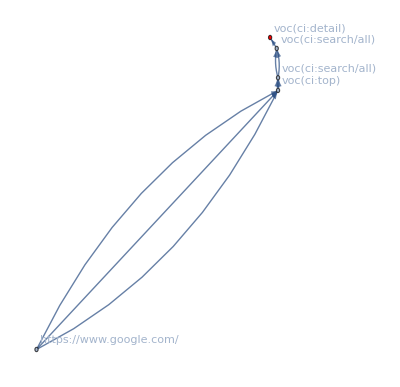

```mathematica
Graph[gr,VertexLabels->vrenameRl]
```

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

```mathematica
toVocGraph[ckanGrPRselHLTL[4][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

-Graphics-

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«117 more identical outputs»

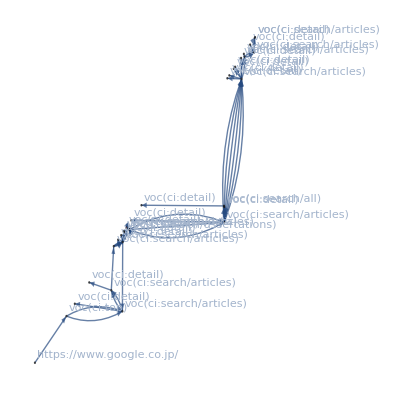
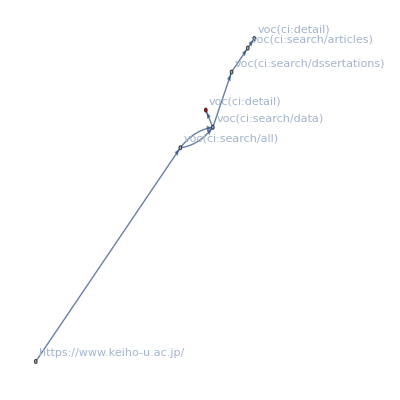
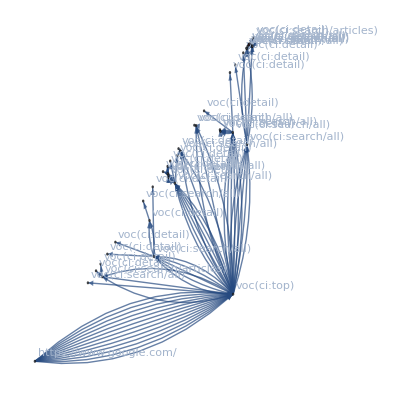
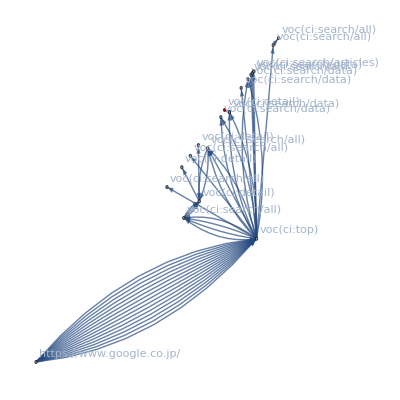
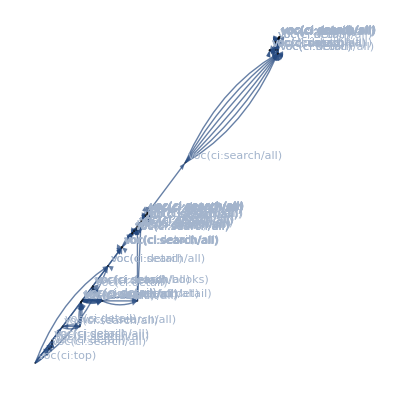
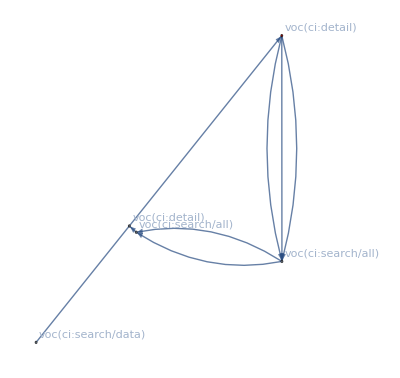
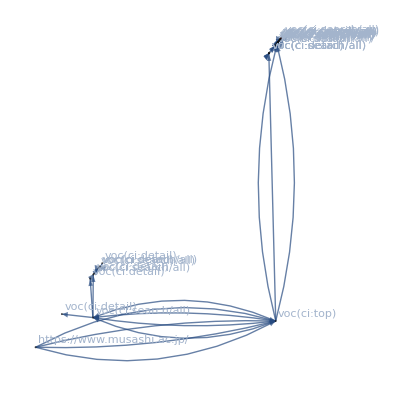
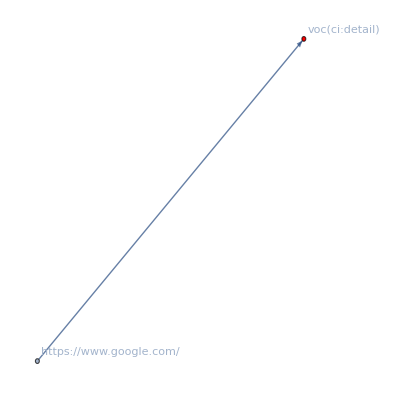
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL[4]]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLogLen[4]}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 21124901
2962926

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 193
11
204 | 166
8
166

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 184333
121

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100
101
102
103
104
105
106
107
108
109
110
111
112
113
114
115
116
117
118
119
120
121 | 888 | 1
5043 | 1
6086 | 1
8845 | 1
8949 | 1
9492 | 1
12443 | 1
12903 | 1
16925 | 1
23064 | 1
23722 | 1
23826 | 1
25863 | 1
26350 | 1
27216 | 1
29045 | 1
30166 | 1
32289 | 1
32493 | 1
41688 | 1
42374 | 1
42580 | 1
42580 | 1
44627 | 1
44627 | 1
44627 | 1
45238 | 1
46599 | 1
50267 | 1
51540 | 1
51540 | 1
54147 | 1
55078 | 1
55874 | 1
55947 | 1
58827 | 1
58830 | 1
58858 | 1
58876 | 1
60551 | 1
60551 | 1
60551 | 1
61029 | 1
61029 | 1
61055 | 1
61599 | 1
61608 | 1
62578 | 1
62578 | 1
62578 | 1
62799 | 1
62945 | 1
63338 | 1
65312 | 1
66102 | 1
69213 | 1
70632 | 1
71995 | 1
71999 | 1
71999 | 1
78100 | 1
78100 | 1
78110 | 1
79940 | 1
79940 | 1
79940 | 1
80300 | 1
81313 | 1
83213 | 1
86213 | 1
89927 | 1
91299 | 1
91299 | 1
91299 | 1
94703 | 1
98403 | 1
98403 | 1
99551 | 1
99551 | 1
99551 | 1
100421 | 1
101044 | 1
101044 | 1
101044 | 1
101044 | 1
101343 | 1
101693 | 1
101693 | 1
101693 | 1
101693 | 1
102713 | 1
102713 | 1
102713 | 1
103863 | 1
104318 | 1
104422 | 1
104422 | 1
104422 | 1
104778 | 1
105480 | 1
105480 | 1
105480 | 1
107743 | 1
107743 | 1
108958 | 1
114524 | 1
116845 | 1
116845 | 1
137416 | 1
137477 | 1
144638 | 1
144806 | 1
147618 | 1
148333 | 1
150444 | 1
150444 | 1
151376 | 1
151376 | 1
151376 | 1
151376 | 1
151962 | 1 | 5
32
7
42
19
104
5
33
2
4
9
6
13
2
6
17
2
6
11
51
2
25
24
99
88
85
19
9
2
39
37
7
13
57
23
9
49
17
38
215
198
10
24
23
26
71
19
22
22
21
7
9
20
25
67
6
17
13
12
11
15
21
11
276
280
272
26
32
8
6
31
189
185
192
3
11
11
44
45
46
14
31
24
24
23
37
106
105
111
106
40
41
45
6
89
14
16
13
5
312
312
318
11
15
2
6
46
45
2
12
22
8
5
2
20
19
295
325
296
296
15 | 8
53
7
96
44
163
7
41
1
3
12
9
16
1
12
42
1
8
15
87
1
62
50
178
129
142
35
12
1
66
51
8
22
75
38
10
83
21
63
323
302
16
52
47
46
128
38
54
45
44
12
10
30
35
99
7
18
20
17
16
17
23
14
396
412
404
49
40
10
5
46
325
311
311
2
15
13
67
68
74
20
45
41
40
35
66
308
284
297
286
51
52
58
6
133
28
29
25
4
501
503
547
20
16
1
10
75
67
1
22
30
11
7
1
34
29
984
1113
986
989
29 | 0.25
24.5333
0.333333
2.48333
0.9
263.133
11.95
114.967
0
0.85
37.8167
0.483333
0.35
0
5.83333
1.
0
10.95
0.733333
1.81667
0
11.3167
11.3167
264.483
421.583
421.583
3.01667
0.25
0
339.933
340.083
1.83333
5.7
13.3167
12.0833
0.75
18.6667
23.2
32.7333
17.3833
17.3833
26.9833
15.15
15.15
36.5833
328.417
17.9
5.23333
5.05
5.23333
7.73333
1.13333
16.05
1.06667
70.8167
4.35
2.63333
15.
167.317
167.317
1.48333
0.916667
341.633
188.233
187.583
188.267
209.1
11.85
505.65
21.7
3.31667
176.35
202.117
202.117
262.583
4.58333
4.58333
121.767
121.767
119.033
4.18333
352.983
218.4
81.2667
81.2667
313.05
59.95
59.95
38.4
59.95
99.0333
99.0333
92.5167
0.816667
369.283
19.55
19.55
19.55
0.9
77.1667
77.1667
92.6333
31.8333
26.9167
0
260.967
294.817
294.817
0
9.53333
10.4167
0.666667
0.716667
0
2.13333
2.61667
39.9167
39.9167
39.9167
39.9167
1.8 | 0.55
47.75
1.28333
22.2667
5.91667
501.95
13.3667
139.383
0.
1.05
39.5833
1.45
2.15
0.
6.63333
7.06667
0.
14.0833
2.2
15.65
0.
36.6167
36.4333
472.083
472.083
472.083
13.4833
1.08333
0.
587.717
587.383
3.18333
20.4
49.4667
18.05
2.25
97.55
52.2333
112.067
68.8333
67.
33.35
22.5333
22.2833
83.35
390.867
34.
24.
23.8
23.8
14.15
2.9
29.7167
8.6
259.267
5.98333
6.83333
20.4
185.017
183.6
5.68333
5.5
580.2
400.633
475.383
399.717
325.033
55.3
508.75
23.1167
22.0333
389.1
261.967
261.967
262.583
7.28333
6.63333
245.117
245.117
281.433
8.85
541.283
406.15
187.567
187.567
457.367
457.283
454.883
457.433
454.883
338.
339.033
338.
1.73333
415.533
33.7333
33.45
33.
1.3
293.917
293.917
449.35
37.05
34.3167
0.
284.617
588.267
587.767
0.
21.4667
48.9833
2.05
1.9
0.
10.75
10.45
147.467
147.467
147.467
147.467
5.51667

### Export:CKAN impact

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{121}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231010/T=4/_story

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910113182970653×10^9

```mathematica
end-start
```

80.217724